```mathematica
kappa0=115
```

115

```mathematica
TOVeqs[rho0_]:=NDSolve[{kappa0*rho'[r]+(M[r]/(2r^2))*(1+kappa0*rho[r])*(1+4*Pi*r^3*kappa0*rho[r]^2/M[r])*(1-2M[r]/r)^(-1)==0,M'[r]==4Pi*rho[r]*r^2,rho[0.001]==rho0,M[0.001]==4Pi*rho0*(0.001)^3/3},{rho,M},{r,0.001,30}]
```

```mathematica
TOVeqs[0.01]
```

{{rho→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

```mathematica
rhoTOV[r_,rho0_]:=rho[r]/.TOVeqs[rho0]
```

```mathematica
MassTOV[r_,rho0_]:=M[r]/.TOVeqs[rho0]
```

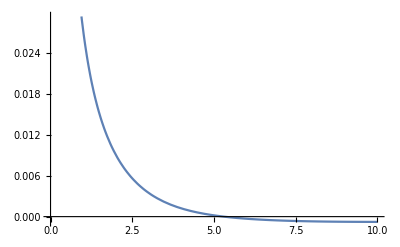

```mathematica
Plot[{rhoTOV[x,10]},{x,0.001,10}]
```

```mathematica
Rstar[rho0_]:=FindRoot[rhoTOV[r,rho0]==0,{r,0.001,20}][[1,2]]
```

```mathematica
Rstar[0.01]
```

6.24755

```mathematica
Mstar[rho0_]:=MassTOV[Rstar[rho0],rho0][[1]]
Mstar[0.01]
```

1.9308

```mathematica
DataMstarRStar = Table[{1.47664*Rstar[10^i],Mstar[10^i]},{i,-4,-1,0.1}];
```

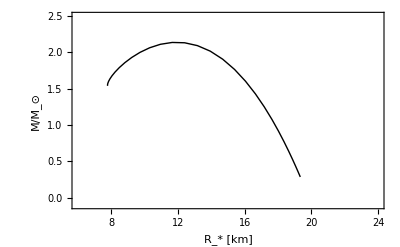

```mathematica
StabTOV =ListLinePlot[DataMstarRStar,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"R_* [km]","M/M_⊙"},LabelStyle->Medium,PlotRange->{{6,24},{-0.1,2.5}}]
```

```mathematica
TOV case. Equation of state: p = Subscript[κ, 0] ρ^2 , taken from arXiv:0309041, with Subscript[κ, 0]= 4.012 × 10^-4 fm^3/MeV.
We use R, p and ρ have dimension of an inverse square length. In this way Subscript[κ, 0]= 2.5 × 10^2 km^2 .
We make everything dimensionless by normalising to half the gravitational radius of the Sun Subscript[r, 0]= 1.47664 km. Therefore Subscript[κ, 0]= 115.
```

Syntax::tsntxi: "TOVcase.Equationofstate:p=κ_0 ρ^2,taken«4»«5»:«7»«1»«1»,pandρhavedimensionofaninversesquarelength.Inthisway κ_0=2.5×10^2 km^2.WemakeeverythingdimensionlessbynormalisingtohalfthegravitationalradiusoftheSun r_0=1.47664km.Therefore κ_0=115." is incomplete; more input is needed.

TOV case. Equation of state: p =  κ_0 ρ^2 , taken from arXiv:0309041, with κ_0= 4.012 × 10^-4 fm^3/MeV.
We use R, p and ρ have dimension of an inverse square length. In this way κ_0= 2.5 × 10^2 km^2.
We make everything dimensionless by normalising to half the gravitational radius of the Sun r_0= 1.47664 km.
Therefore κ_0= 115.

```mathematica
M ={ [([3(5)^3])/(2^9)^(1/4)]*[(hc/G)^(3/2)]*[1/(pi*m^2)]}
```

```mathematica
M
```

M

```mathematica
x^2+x^(-1)+Pi
```

π+1/x+x^2

```mathematica
((((3(5)^3))/(2^9)^(1/4))*((hc/G)^(3/2))*(1/(pi*m^2)))
```

(375 (hc/G)^(3/2))/(4 2^(1/4) m^2 pi)

```mathematica
M_unstable>((((3(5)^3))/(2^9)^(1/4))*((hc/G)^(3/2))*(1/(pi*m^2)))
```

M_unstable>(375 (hc/G)^(3/2))/(4 2^(1/4) m^2 pi)

```mathematica
ctrl= speed of light
```

light of speed

```mathematica
LinguisticAssistant["Value"]
```

(1 c)[Value]

```mathematica
LinguisticAssistant
```

1 c

```mathematica
LinguisticAssistant["Value"]
```

(1 c)[Value]

```mathematica
LinguisticAssistant ["Value"]
```

(1 N_A)[Value]

```mathematica
Entity["PhysicalConstant","AvogadroConstant"]["Value"]
```

602214076000000000000000 /mol

```mathematica
LinguisticAssistant["Value"]
```

299792458 m/s

```mathematica
LinguisticAssistant["Value"]
```

132521403/200000000000000000000000000000000000000000 s J

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant["Value"]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant["Value"]
```

Missing[UnknownProperty,{Particle,Value}]

```mathematica
LinguisticAssistant["Properties"]
```

{antiparticle,baryon number,bottomness,electric charge,electric charge,root mean square charge radius,charge states,charm,classical radius,Compton wavelength,charge conjugation,decay modes,decay type,electric charge density,entity classes,excitations,decay modes,full symbol,generic full symbol,generic symbol,spin g-factor,G-parity,half-life,hypercharge,isospin,isospin, G parity,isospin multiplet,isospin partners,isospin projection,lepton number,mean lifetime,mass,mass density,mean square charge radius,memberships,name,parity,interactions studied,PDG number,constituent quarks,quark model angular momentum state,quark content orbital angular momentum quantum number (L),quark content total spin quantum number (S),radioactivity,radius,spin,spin-parity,spin, parity, C parity,particle statistics,strangeness,symbol,topness,particle type,unobserved decay modes,width}

```mathematica
LinguisticAssistant["Mass"]
```

939.5654133 MeV/c^2

```mathematica
m = LinguisticAssistant["Mass", kg]
```

939.5654133 MeV/c^2

```mathematica
m
```

939.5654133 MeV/c^2

```mathematica
c=LinguisticAssistant["Value"]
```

299792458 m/s

```mathematica
c
```

299792458 m/s

```mathematica
h= LinguisticAssistant["Value"]
```

132521403/200000000000000000000000000000000000000000 s J

```mathematica
h
```

132521403/200000000000000000000000000000000000000000 s J

```mathematica
M_unstable>((((3(5)^3))/(2^9)^(1/4))*((h*c/G)^(3/2))*(1/(pi*m^2)))
```

M_unstable>(((19864458571489287/100000000000000000000000000000000000000000 m J)/G)^(3/2) (0.0000893017017 c^4/MeV^2))/pi

```mathematica
G=LinguisticAssistant["Value"]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
M_unstable>((((3(5)^3))/(2^9)^(1/4))*((h*c/G)^(3/2))*(1/(Pi*m^2)))
```

M_unstable>0.1798 kg^(3/2)s^3 c^4/(m^3 √J)

```mathematica
LinguisticAssistant["Mass"]
```

1.988435×10^30 kg

```mathematica
clear[m]
```

clear[939.5654133 MeV/c^2]

```mathematica
Clear[m]
```

```mathematica
Needs["PhysicalConstants`"]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
m = LinguisticAssistant ["MassUnit"]
```

Missing[UnknownProperty,{Particle,MassUnit}]

```mathematica
ClearAll
```

ClearAll

```mathematica
m = 1.80 x (10^-28) ["MassUnit"]
```

1.8 x 1/10000000000000000000000000000[MassUnit]

```mathematica
LinguisticAssistant ["Mass"]
```

1.988435×10^30 kg

```mathematica
Clear[m]
```

```mathematica
m = LinguisticAssistant ["Mass"->"MassUnit"]
```

neutron[Mass→MassUnit]

```mathematica
Clear[m]
```

```mathematica
UnitSimplify[LinguisticAssistant ,UnityDimensions->{"MassUnit"}]
```

neutron

```mathematica
UnitSimplify[LinguisticAssistant ["Mass"],UnityDimensions->{"MassUnit"}]
```

1.674927485×10^-27

```mathematica
m= UnitSimplify[LinguisticAssistant ["Mass"],UnityDimensions->{"MassUnit"}]
```

1.674927485×10^-27

```mathematica
c=LinguisticAssistant["Value"]
```

299792458 m/s

```mathematica
h= LinguisticAssistant["Value"]
```

132521403/200000000000000000000000000000000000000000 s J

```mathematica
G=LinguisticAssistant["Value"]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
M_unstable>((((3(5)^3))/(2^9)^(1/4))*((h*c/G)^(3/2))*(1/(Pi*m^2)))
```

M_unstable>1.452×10^33 kg^(3/2)s^3 J^(3/2)/m^3

```mathematica
ClearAll
```

ClearAll

```mathematica
m
```

1.674927485×10^-27

```mathematica
Clear[m]
```

```mathematica
m
```

m

```mathematica
Clear[m,h,G,M]
```

```mathematica
R := (3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(M^(-1/3))
```

```mathematica
R
```

(3 (3/2)^(1/3) h^2)/(8 G m^(8/3) M^(1/3) π^(4/3))

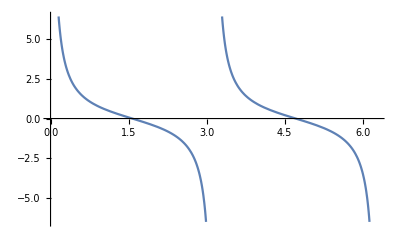

```mathematica
Plot[Cot[x],{x,0,2π}]
```

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}]
```

-Graphics-

```mathematica
m= UnitSimplify[LinguisticAssistant ["Mass"],UnityDimensions->{"MassUnit"}]
c=LinguisticAssistant["Value"]
h= LinguisticAssistant["Value"]
G=LinguisticAssistant["Value"]
```

1.674927485×10^-27

299792458 m/s

132521403/200000000000000000000000000000000000000000 s J

6.674×10^-11 m^3/(kg s^2)

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}]
```

-Graphics-

```mathematica
Clear[m]
```

```mathematica
m = LinguisticAssistant["Mass"]
```

939.5654133 MeV/c^2

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}]
```

-Graphics-

```mathematica
kappa0*rho'[r]+(M[r]/(2r^2))*(1+kappa0*rho[r])*(1+4*Pi*r^3*kappa0*rho[r]^2/M[r])*(1-2M[r]/r)^(-1)
```

(M[r] (1+115 rho[r]) (1+(460 π r^3 rho[r]^2)/M[r]))/(2 r^2 (1-(2 M[r])/r))+115 rho'[r]

```mathematica
M'[r]==4Pi*rho[r]*r^2
```

M'[r]==4 π r^2 rho[r]

```mathematica
s=NDSolve[{y'[x]==y[x] Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

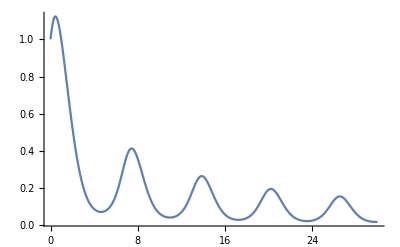

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

```mathematica
p= NDSolve[{rho''[r]==-((alpha*rho'[r]^(1/Gamma)*M'[r])/(r^2)),rho'[R]==0, M'[r]==4Pi*rho[r]*r^2, M[0.001]==4Pi*rho0*(0.001)^3/3},rho,{r,0,100}]
```

NDSolve::ndsv: Cannot find starting value for the variable rho.

NDSolve[{rho''[r]==-(alpha M'[r] rho'[r]^(1/Gamma))/r^2,rho'[R]==0,M'[r]==4 π r^2 rho[r],M[0.001]==4.18879×10^-9 rho0},rho,{r,0,100}]

```mathematica
NDSolve[{kappa0*rho'[r]+(M[r]/(2r^2))*(1+kappa0*rho[r])*(1+4*Pi*r^3*kappa0*rho[r]^2/M[r])*(1-2M[r]/r)^(-1)==0,M'[r]==4Pi*rho[r]*r^2,rho[0.001]==rho0,M[0.001]==4Pi*rho0*(0.001)^3/3},{rho,M},{r,0.001,30}]
```

NDSolve::ndinnt: Initial condition 4.18879×10^-9 rho0 is not a number or a rectangular array of numbers.

NDSolve[{(M[r] (1+kappa0 rho[r]) (1+(4 kappa0 π r^3 rho[r]^2)/M[r]))/(2 r^2 (1-(2 M[r])/r))+kappa0 rho'[r]==0,M'[r]==4 π r^2 rho[r],rho[0.001]==rho0,M[0.001]==4.18879×10^-9 rho0},{rho,M},{r,0.001,30}]

```mathematica
kappa0=115
TOVeqs[rho0_]:=NDSolve[{kappa0*rho'[r]+(M[r]/(2r^2))*(1+kappa0*rho[r])*(1+4*Pi*r^3*kappa0*rho[r]^2/M[r])*(1-2M[r]/r)^(-1)==0,M'[r]==4Pi*rho[r]*r^2,rho[0.001]==rho0,M[0.001]==4Pi*rho0*(0.001)^3/3},{rho,M},{r,0.001,30}]
TOVeqs[0.01]
```

115

{{rho→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

```mathematica
?NDSolve
```

```mathematica
m = LinguisticAssistant["Mass"]
```

939.5654133 MeV/c^2

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}]
```

-Graphics-

```mathematica
c=LinguisticAssistant["Value"]
h= LinguisticAssistant["Value"]
G=LinguisticAssistant["Value"]
```

299792458 m/s

132521403/200000000000000000000000000000000000000000 s J

6.674×10^-11 m^3/(kg s^2)

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Kg,y}]
```

-Graphics-

```mathematica
Clear[m]
```

```mathematica
m = UnitConvert[Quantity[LinguisticAssistant,"Mass"],"Kilograms"]
```

Quantity::unkunit: Unable to interpret unit specification Mass.

General::stop: Further output of Quantity::unkunit will be suppressed during this calculation.

Quantity::compat: Mass and Kilograms are incompatible units

$Failed

```mathematica
Clear[m]
```

```mathematica
m=LinguisticAssistant ["Mass"]
```

939.5654133 MeV/c^2

```mathematica
n = 1.675 * 10^(-27) kg
```

1.675×10^-27 kg

```mathematica
UnitConvert[m, "Kilograms"]
```

1.674927485×10^-27 kg

```mathematica
Clear[m,n]
```

```mathematica
n = LinguisticAssistant ["Mass"]
```

939.5654133 MeV/c^2

```mathematica
m = UnitConvert[n, "Kilograms"]
```

1.674927485×10^-27 kg

```mathematica
R := (3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3))
```

```mathematica
R
```

(1.551×10^14 s^4 J^2/(kg^(5/3)m^3))/x^(1/3)

```mathematica
Clear[R]
```

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33 "Kilograms"}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Kg,y}]
```

Plot::plln: Limiting value 1000000000000000000000000000000000 Kilograms in {x,0,1000000000000000000000000000000000 Kilograms} is not a machine-sized real number.

Plot[(3 ((3/2)^(1/3) h^2) x^(-1/3))/(8 (G π^(4/3) m^(8/3))),{x,0,10^33 Kilograms},PlotStyle→{Blue,Thick},Frame→True,FrameLabel→{Kg,y}]

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33 kg}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Kg,y}]
```

Plot::plln: Limiting value 1000000000000000000000000000000000 kg in {x,0,1000000000000000000000000000000000 kg} is not a machine-sized real number.

Plot[(3 ((3/2)^(1/3) h^2) x^(-1/3))/(8 (G π^(4/3) m^(8/3))),{x,0,10^33 kg},PlotStyle→{Blue,Thick},Frame→True,FrameLabel→{Kg,y}]

```mathematica
Clear [c]
```

```mathematica
c = Quantity[299792458, ("Meters")/("Seconds")]
```

299792458 m/s

299792458 m/s

```mathematica
Clear[c]
```

```mathematica
m = 1.674927485 * 10^(-27)
```

1.67493×10^-27

```mathematica
c= 299792458
```

299792458

```mathematica
h = 132521403/200000000000000000000000000000000000000000
```

132521403/200000000000000000000000000000000000000000

```mathematica
clear[h]
```

clear[132521403/200000000000000000000000000000000000000000]

```mathematica
Clear[h]
```

```mathematica
h = 6.62607004081818181818181 * 10^(-34)
```

6.6260700408181818181818×10^-34

```mathematica
G =6.674 * 10^(-11)
```

6.674×10^-11

```mathematica
Plot[(3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3)),{x, 0,10^33}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Kg,m}]
```

-Graphics-

```mathematica
y = (3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(m^(8/3))))*(x^(-1/3))
```

(1.55119×10^14)/x^(1/3)

```mathematica
Plot[y,{x, 0,10^33}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Kg, Radius (m)}]
```

-Graphics-

```mathematica
Clear[m]
```

```mathematica
n= 1.674927485 * 10^(-27)
```

1.67493×10^-27

```mathematica
y = (3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(n^(8/3))))*(x^(-1/3))
```

(1.55119×10^14)/x^(1/3)

```mathematica
Plot[y,{x, 0,10^33},{y, 0, 10^9}, PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{"Mass (kg)", "Radius (m)"}]
```

Plot::nonopt: Options expected (instead of {y,0,10^9}) beyond position 2 in Plot[y,{x,0,10^33},{y,0,10^9},PlotStyle→{Blue,Thick},Frame→True,FrameLabel→{Mass (kg),Radius (m)}]. An option must be a rule or a list of rules.

Plot[y,{x,0,10^33},{y,0,10^9},PlotStyle→{Blue,Thick},Frame→True,FrameLabel→{Mass (kg),Radius (m)}]

```mathematica
Clear[y]
```

```mathematica
R = (3/8)*(((3/2)^(1/3)(h^2))/(G(Pi^(4/3))(n^(8/3))))*(x^(-1/3))
```

(1.55119×10^14)/x^(1/3)

```mathematica
Plot[R,{x,0,10^33},PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{"Mass (kg)","Radius (m)"}, PlotLabel-> "Equilibrium Radius vs Star Mass"]
```

-Graphics-